## Derive Functional Equation Tools

```mathematica
BeginPackage["QMeSderivation`Tools`"]
```

## Exports

```mathematica
ReduceIdenticalFlowDiagrams::usage = "ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.
";
```

```mathematica
PlotSuperindexDiagram::usage = "PlotSuperindexDiagram[diagram, setup, options]

Plot a single superindex diagram. The first argument to this function is the diagram itself, the second one is a valid QMeS setup.
The diagram has to be a superindex diagram.

The options for the function PlotSuperindexDiagram are:
\"ShowEdgeLabels\" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
\"EdgeStyle\" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		\"EdgeStyle\"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.
";
```

```mathematica
PlotSuperindexDiagrams::usage="PlotSuperindexDiagram[diagrams, setup, options]

Plot a set of superindex diagrams. The first argument to this function is a list of diagrams, the second one is a valid QMeS setup.
The diagrams have to be superindex diagrams.

The options for the function PlotSuperindexDiagrams are:
\"ShowEdgeLabels\" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
\"EdgeStyle\" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		\"EdgeStyle\"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.
"
```

```mathematica
Begin["`Private`"]
```

## Debug

```mathematica
$DebugLevel =0;
```

```mathematica
myEcho[msg_,lvl_] := If[$DebugLevel >=lvl, Echo[msg];, Nothing;]
```

## Utilities

### Tests and assertions

```mathematica
TestIsSuperindexDiagram[diag_]:=Module[{hasPrefactor,hasAssociations},
If[Not[ListQ[diag]&&Length[diag]>1],Return[False]];
hasAssociations=AllTrue[Map[AssociationQ,Flatten@diag[[2;;]]],Identity]&&Length[Flatten@diag[[2;;]]]>0;
hasPrefactor=Extract[diag[[1]],1]=="Prefactor";
Return[hasAssociations&&hasPrefactor]
]
AssertIsSuperIndexDiagram[diag_,context_String:""]:=If[Not@TestIsSuperindexDiagram[diag],Print[context," Argument is not a SuperIndexDiagram."];Abort[]];
AssertAllSuperIndexDiagrams[diags_List,context_String:""]:=Map[AssertIsSuperIndexDiagram[#,context]&,diags];
```

```mathematica
TestIsOneLoop[diag_]:=Module[{internalIndices,objectIndices,assignNumber,mapAssignNumber,testNumbers},
AssertIsSuperIndexDiagram[diag,"TestIsOneLoop:"];

(*An expression is one-loop if every object (vertex or propagator) has only one incoming and one outgoing index.
Therefore, what we do here is to check the number of internal indices of any object in the diagram and testing whether this is exactly 2 for all objects.*)

internalIndices=GetInternalIndices[diag];
objectIndices=Map[#["indices"]&,diag[[2;;]]];

assignNumber=If[MemberQ[internalIndices,#],1,0]&;
mapAssignNumber=Map[assignNumber,#]&;
testNumbers=Map[Total[mapAssignNumber[#]]&,objectIndices];
Return[AllTrue[testNumbers,#==2&]]
];
AssertIsOneLoop[diag_List,context_String:""]:=If[Not@TestIsOneLoop[diag],Print[context," Diagram is not one-loop."];Abort[]];

TestIsFlowDiagram[diag_]:=Module[{content,regulatordotMatch},
content=SuperIndexDiagramContent[diag];
regulatordotMatch=Select[content,StringMatchQ[#,"Regulatordot"~~___]&];
If[Length[regulatordotMatch]==1,True,False]
];
AssertIsFlowDiagram[diag_List,context_String:""]:=If[Not@TestIsFlowDiagram[diag],Print[context," Diagram is not a flow diagram."];Abort[]];
```

### Getting objects

```mathematica
GetIndices[diag_List]:=Module[{},
AssertIsSuperIndexDiagram[diag,"TestIsOneLoop:"];
Flatten[Map[#["indices"]&,diag[[2;;]]],1]
];
GetExternalIndices[diag_List]:=Module[{allIndices},
AssertIsSuperIndexDiagram[diag,"TestIsOneLoop:"];
allIndices=GetIndices[diag];
Keys@Select[Counts[allIndices],#==1&]
];
GetInternalIndices[diag_List]:=Module[{allIndices},
AssertIsSuperIndexDiagram[diag,"TestIsOneLoop:"];
allIndices=GetIndices[diag];
Keys@Select[Counts[allIndices],#>1&]
];

GetIndices[obj_Association]:=Module[{},
obj["indices"]
];
GetExternalIndices[diag_List,obj_Association]:=Module[{allIndices,externalIndices},
allIndices=GetIndices[obj];
externalIndices=GetExternalIndices[diag];
Select[allIndices,MemberQ[externalIndices,#]&]
];
GetInternalIndices[diag_List,obj_Association]:=Module[{allIndices,internalIndices},
AssertIsSuperIndexDiagram[diag,"TestIsOneLoop:"];
allIndices=GetIndices[obj];
internalIndices=GetInternalIndices[diag];
Select[allIndices,MemberQ[internalIndices,#]&]
];
```

```mathematica
GetObjectIdentifier[ob_Association]:=Module[{},
ob["type"]<>StringJoin[Map[ToString[#[[1]]]&,ob["indices"]]]
];

GetRegulatordot[diag_]:=Module[{},
AssertIsFlowDiagram[diag,"GetRegulatordot:"];
Select[diag,MemberQ[#,"Regulatordot",Infinity]&][[1]]
];
```

```mathematica
GetBosons[setup_Association]:=Map[Head,setup["FieldSpace"]["bosonic"]];
GetFermionPairs[setup_Association]:=Map[{Head[#[[1]]],Head[#[[2]]]}&,setup["FieldSpace"]["fermionic"]];
GetFermions[setup_Association]:=Map[Head[#[[2]]]&,setup["FieldSpace"]["fermionic"]];
GetAntiFermions[setup_Association]:=Map[Head[#[[1]]]&,setup["FieldSpace"]["fermionic"]];
```

## Diagram reduction

### Diagram grouping

```mathematica
SuperIndexDiagramContent[diag_]:=Module[{},
AssertIsSuperIndexDiagram[diag,"SuperIndexDiagramContent:"];
Sort[Map[GetObjectIdentifier,diag[[2;;]]]]
];
SeparateSuperIndexDiagramGroups[diags_List]:=Module[{identifierRep,removeFirsts,groupedDiagrams},
AssertAllSuperIndexDiagrams[diags,"SeparateSubdiagramGroups:"];

(*We group all diagrams into groups that could be potentially identical. 
We simply make sure that in each group all diagrams have the same objects, ignoring topology.*)
identifierRep=Map[SuperIndexDiagramContent,diags];
identifierRep=Thread[{identifierRep,diags}];
removeFirsts[ex_]:=Map[#[[2]]&,ex];
groupedDiagrams=Map[removeFirsts,GatherBy[identifierRep,#[[1]]&]];

Return[groupedDiagrams]
];
```

### Comparison of two diagrams

```mathematica
IterateDiagram[diag_,curPos_,entryIdx_]:=Module[{curIdxs,exitIdx,nextPos,externalIndices,i,candidates},
(*Given a superindex diagram diag, find the entry (curPos) in the diagram. Then, remove the entryIdx from this entry, grab the next index (exitIxd),
  and find the next entry (nextPos) which is connected by this exitIdx.*)

curIdxs=curPos["indices"];
If[Not@MemberQ[curIdxs,entryIdx],Print["IterateDiagram: Invalid entryIdx"];Abort[]];
externalIndices=GetExternalIndices[diag];
For[i=1,i<=Length[externalIndices],i++,curIdxs=DeleteCases[curIdxs,externalIndices[[i]]]];
exitIdx=DeleteCases[curIdxs,entryIdx][[1]];

candidates=Select[diag[[2;;]],MemberQ[#,exitIdx,Infinity]&];
If[Length[candidates]!=2,Print["IterateDiagram: Logic Error"];Abort[]];
nextPos=DeleteCases[candidates,curPos][[1]];

Return[{nextPos,exitIdx}];
];

CheckOneLoopDiagramIdentity[indiag1_,indiag2_,symmetryList_List:{}]:=Module[{startPos,CheckIteration,entryIdx,diag1,diag2,symmidx,sign},
(*Given two one-loop diagrams, start in both at the regulator. 
Then, step through the diagrams (at the same time) in one direction and compare whether they are identical.
Do this several times: Both directions and utilizing (one after the other) all symmetry transformations (symmetries).
If any of these procedures matches perfectly, return True. Otherwise, return always False. 
*)
AssertIsOneLoop[indiag1,"CheckDiagramIdentity:"];
AssertIsOneLoop[indiag2,"CheckDiagramIdentity:"];

CheckIteration[entry_]:=Module[{curPos,curIdx,iter,externalIndices={0,0},objectIdentifiers={"",""}},
curPos=startPos;
curIdx=entry;
iter=0;


While[(iter==0||curPos!=startPos)&&iter<50,

externalIndices[[1]]=GetExternalIndices[diag1,curPos[[1]]];
externalIndices[[2]]=GetExternalIndices[diag2,curPos[[2]]];

objectIdentifiers[[1]]=GetObjectIdentifier[curPos[[1]]];
objectIdentifiers[[2]]=GetObjectIdentifier[curPos[[2]]];

If[externalIndices[[1]]=!=externalIndices[[2]],myEcho["Diff: ",externalIndices[[1]]," vs ",externalIndices[[2]],2];Return[False]];
If[objectIdentifiers[[1]]=!=objectIdentifiers[[2]],myEcho["Diff: ",objectIdentifiers[[1]]," vs ",objectIdentifiers[[2]],2];Return[False]];

{curPos[[1]],curIdx[[1]]}=IterateDiagram[diag1,curPos[[1]],curIdx[[1]]];
{curPos[[2]],curIdx[[2]]}=IterateDiagram[diag2,curPos[[2]],curIdx[[2]]];
iter++;
];
If[iter>=50,Return[False]];

Return[True]
];

For[symmidx=0,symmidx<=Length[symmetryList],symmidx++,
diag1=indiag1;
If[symmidx>0,diag2=indiag2/.symmetryList[[symmidx]]["Rule"],diag2=indiag2];
If[symmidx>0,
sign=If[symmetryList[[symmidx]]["Sign"]===Plus,1,-1],
sign=1];

startPos=Map[GetRegulatordot,{diag1,diag2}];

entryIdx=Map[#["indices"][[1]]&,startPos];
If[entryIdx[[1,1]]==entryIdx[[2,1]],
If[CheckIteration[entryIdx],Return[{True,sign}]];
];

entryIdx[[2]]=startPos[[2]]["indices"][[2]];
If[entryIdx[[1,1]]==entryIdx[[2,1]],
If[CheckIteration[entryIdx],Return[{True,sign}]];
];
];

Return[{False,0}]
];
```

### Diagram set reduction

```mathematica
BuildSymmetryList[symmetries_,derivativeList_]:=Module[{procDerList,buildOneSymmetry},
If[Head[symmetries]=!=List,Print["Symmetries must be given as a list!"];Abort[]];
If[Length[symmetries]==0,Return[{}]];
If[Length[derivativeList]==0,Return[{}]];

procDerList=Map[{Head[#],List@@#}&,derivativeList];

buildOneSymmetry[sym_]:=Module[{valid=True,buildCycle,pairs},
If[sym[[-1]]=!=Plus&&sym[[-1]]=!=Minus,valid=False];
If[AnyTrue[sym[[;;-2]],Not[Head[#]===List]&],valid=False];
pairs=Subsets[sym[[;;-2]],{2}];
valid=Not@AnyTrue[Map[ContainsAny[#[[1]],#[[2]]]&,pairs],Identity];
If[Not@valid,Print[sym," is  not a valid symmetry!"];Abort[]];

buildCycle[cyc_]:=Module[{cycvalid=True,numberRules,idx,nextIdx},
If[AnyTrue[cyc,Not[IntegerQ[#]]&],cycvalid=False];
If[AnyTrue[cyc,(#>Length[derivativeList])||(#<1)&],cycvalid=False];
If[Not@cycvalid,Print[cyc," is  not a valid cycle!"];Abort[]];

numberRules={};
For[idx=1,idx<=Length[cyc],idx++,
nextIdx=Mod[(idx),Length[cyc]]+1;
numberRules=Join[numberRules,{{cyc[[idx]],cyc[[nextIdx]]}}];
];

Return[Map[procDerList[[#[[1]]]]->procDerList[[#[[2]]]]&,numberRules]];
];

<|
"Rule"->Flatten[Map[buildCycle,sym[[;;-2]]],1],
"Sign"->sym[[-1]]
|>
];

Map[buildOneSymmetry,symmetries]
];
```

```mathematica
ReduceIdenticalFlowDiagrams[diags_,derivativeList_:{},symmetries_List:{}]:=Module[{separatedGroups,reduceGroup,reducedGroups,symmetryList},
AssertAllSuperIndexDiagrams[diags,"ReduceIdenticalFlowDiagrams"];

separatedGroups=SeparateSuperIndexDiagramGroups[diags];
symmetryList=BuildSymmetryList[symmetries,derivativeList];

reduceGroup[groupDiags_]:=Module[{i,j,multiplicities,identitiesSigns,signs,identities,prefactors,newDiags},
multiplicities=Table[1,{i,Length[groupDiags]}];
For[i=1,i<=Length[groupDiags],i++,
If[multiplicities[[i]]>0,
identitiesSigns=Table[{False,0},{k,i+1,Length[groupDiags]}];
For[j=i+1,j<=Length[groupDiags],j++,
If[multiplicities[[j]]>0,
identitiesSigns[[j-i]]=CheckOneLoopDiagramIdentity[groupDiags[[i]],groupDiags[[j]],symmetryList];
];
];
signs=Map[If[#[[1]],#[[2]],0]&,identitiesSigns];
identities=Map[If[#[[1]],1,0]&,identitiesSigns];
identities=Join[
Table[0,{j,i-1}],
{Total[signs]},
-identities];
multiplicities=multiplicities+identities;
];
];

prefactors=Map["Prefactor"/.#[[1]]&,groupDiags];
prefactors=multiplicities*prefactors;

newDiags=groupDiags;

For[i=1,i<=Length[groupDiags],i++,
newDiags[[i]][[1]]=("Prefactor"->prefactors[[i]]);
];
newDiags=Select[newDiags,("Prefactor"/.#[[1]])=!={0}&];

Return[newDiags];
];

reducedGroups=ParallelMap[reduceGroup,separatedGroups];

Return[Flatten[reducedGroups,1]];
];
```

32

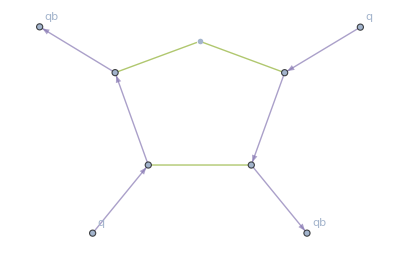
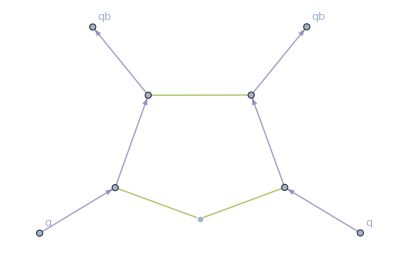
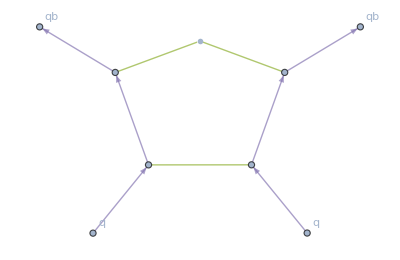
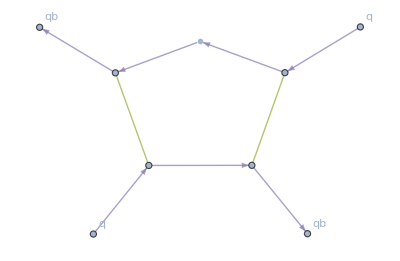
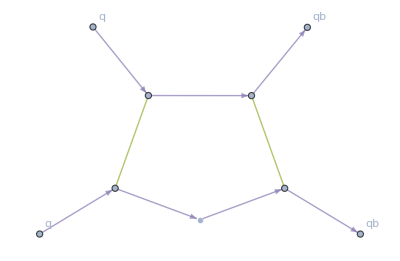
{{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{-4,-Graphics-},{-4,-Graphics-}}

```mathematica
Diagramsqbqqbq=Select[Import["./diagramsqbqqbq.m"],Not[MemberQ[#,Π,Infinity]]&&Not[MemberQ[#,σ,Infinity]]&];
DerivativeListqbqqbq= {qb[p4,{d4,c4,f4}],q[p3,{d3,c3,f3}],qb[p2,{d2,c2,f2}],q[p1,{p1,c1,f1}]};
Diagramsqbqqbq//Length
symm={
{{1,3},Plus},
{{2,4},Plus},
{{1,3},{2,4},Plus}
};
res=ReduceIdenticalFlowDiagrams[Diagramsqbqqbq,DerivativeListqbqqbq,symm];
PlotSuperindexDiagrams[res,SetupfRG]
```

## Diagram drawing

```mathematica
GetPartnerField[field_,setup_]:=Module[{fermions,bosons,sel},
fermions=GetFermionPairs[setup];
bosons=GetBosons[setup];

If[MemberQ[fermions,field,Infinity],
sel=Select[fermions,MemberQ[#,field,Infinity]&][[1]];
sel=DeleteCases[sel,field];
Return[sel[[1]]];
];

If[MemberQ[bosons,field,Infinity],
Return[field]
];

Print["field ",field," not found!"];
Abort[];
];

GetEdgeRule[obj_,fields_,setup_]:=Module[{fermions,bosons,sel},
If[Length[obj]!=Length[fields]||Length[obj]!=2,Print["Mismatch!"];Abort[]];
fermions=GetFermionPairs[setup];
bosons=GetBosons[setup];

If[MemberQ[fermions,fields[[1]],Infinity]&&MemberQ[fermions,fields[[2]],Infinity],
sel=Select[fermions,MemberQ[#,fields[[1]],Infinity]&][[1]];
If[fields===sel,
Return[obj[[1]]->obj[[2]]],
Return[obj[[2]]->obj[[1]]];
]
];

If[MemberQ[bosons,fields[[1]],Infinity]&&MemberQ[bosons,fields[[2]],Infinity],
Return[obj[[1]]<->obj[[2]]]
];

Print["fields ",fields," not found!"];
Abort[];
];
```

```mathematica
MakeEdgeStyle[style_,setup_]:=Module[{corStyle,havePairs,allPairs,missingPairs},
corStyle=style/.{
a_[c_,d_]/;
a===Rule&&Head[c]=!=List:>
Sort[{c,GetPartnerField[c,setup]}]->d};
corStyle=corStyle/.{a_[{c__},d_]/;a===Rule:>Sort[{c}]->d};

havePairs=corStyle/.{a_[{c__},d_]/;a===Rule:>{c}};
allPairs=Join[Map[{#,#}&,GetBosons[setup]],Map[Sort,GetFermionPairs[setup]]];
missingPairs=DeleteCases[allPairs,Alternatives@@havePairs];
corStyle=Join[corStyle,Thread[missingPairs->ColorData[97,"ColorList"][[1;;Length[missingPairs]]]]];
Return[corStyle]
];
```

```mathematica
PlotSuperindexDiagram[diag_,setup_,OptionsPattern[]]:=Module[
{ShowEdgeLabels,EdgeStyle,
transformedDiag,vertices,edges,prefactor,
externalLegs,externalIndices,idx,field,partnerField,outerIdx,externalLeg,
regulatorVertex,curVertex,rules,corStyle,cross,
explVertices,explEdges,vertexShapes,vertexLabels,edgeLabels},

AssertIsSuperIndexDiagram[diag];

EdgeStyle=OptionValue["EdgeStyle"];
ShowEdgeLabels=OptionValue["ShowEdgeLabels"];

transformedDiag=Map[
If[Head[#]===Association,
If[#["type"]=="Propagator",
<|
"Rule"->GetEdgeRule[{#["indices"][[1,2]],#["indices"][[2,2]]},{#["indices"][[1,1]],#["indices"][[2,1]]},setup],
"Style"->Sort[{#["indices"][[1,1]],#["indices"][[2,1]]}]
|>,
<|
"Vertex"->#["indices"][[All,2]],
"Style"->#["type"]
|>],
#]&
,diag];

vertices=Select[transformedDiag,MemberQ[Keys[#],"Vertex",Infinity]&];
edges=Select[transformedDiag,MemberQ[Keys[#],"Rule",Infinity]&];
prefactor=("Prefactor"/.transformedDiag[[1]])[[1]];

externalLegs=GetExternalIndices[diag];
externalIndices={};
For[idx=1,idx<=Length[externalLegs],idx++,
field=externalLegs[[idx,1]];
partnerField=GetPartnerField[field,setup];
outerIdx=Unique[externalLeg];
externalIndices=Join[externalIndices,{outerIdx}];
vertices=vertices∪{<|
"Vertex"->{{outerIdx}},
"Style"->externalLeg[field]
|>};
edges=edges∪{<|
"Rule"->GetEdgeRule[{externalLegs[[idx,2]],{outerIdx}},{field,partnerField},setup],"Style"->Sort[{field,partnerField}]
|>};
];

regulatorVertex=0;
For[idx=1,idx<=Length[vertices],idx++,
curVertex=vertices[[idx]]["Vertex"];
If[Length[curVertex]>1,
rules=Map[#->curVertex[[1]]&,curVertex[[2;;]]];
vertices=vertices/.rules;
edges=edges/.rules;
];
vertices[[idx]]=<|"Vertex"->vertices[[idx]]["Vertex"][[1]],"Style"->vertices[[idx]]["Style"]|>;
If[vertices[[idx]]["Style"]=="Regulatordot",regulatorVertex=vertices[[idx]]["Vertex"]];
];

corStyle=MakeEdgeStyle[EdgeStyle,setup];

 cross[r_] := Graphics[{Thick, Line[{{r / Sqrt[2], r / Sqrt[2]
            }, {-r / Sqrt[2], -r / Sqrt[2]}}], Line[{{r / Sqrt[2], -r / Sqrt[2]},
             {-r / Sqrt[2], r / Sqrt[2]}}], Circle[{0, 0}, r]}];

explVertices=Map[#["Vertex"]&,vertices];
vertexShapes=Join[
{regulatorVertex->cross[1]}
];
vertexLabels=Map[
#["Vertex"]->(#["Style"]/.a_[b_]:>b)&
,
Select[vertices,Head[#["Style"]]===externalLeg&]
];
explEdges=Map[Style[#["Rule"],#["Style"]/.corStyle]&,edges];
edgeLabels=If[ShowEdgeLabels,
Map[#["Rule"]->ToString[#["Style"][[1]]]<>ToString[#["Style"][[2]]]&,edges],
{}
];

Return[
{prefactor,
Graph[explVertices,explEdges,
VertexShape->vertexShapes,
VertexLabels->vertexLabels,
VertexSize -> {regulatorVertex -> Medium},
EdgeLabels->edgeLabels
]
}
];
];
Options[PlotSuperindexDiagram]={"ShowEdgeLabels"->False,"EdgeStyle"->{}};
PlotSuperindexDiagrams[diags_List,setup_,a___]:=Module[{},
Map[PlotSuperindexDiagram[#,setup,a]&,diags]
];
```

## Testing

```mathematica
Needs["QMeSderivation`"]
fRGEq = {"Prefactor"->{1/2},
<|"type"->"Regulatordot", "indices"->{i,j}|>,
<|"type"->"Propagator", "indices"->{i,j}|>};

fieldsNf2p1 = <|"bosonic"-> {σ[p],Π[p,{a}], A[p,{v, c}]},
                 "fermionic"->{{sb[p,{d,c}],s[p,{d,c}]},{qb[p,{d,c,f}],q[p,{d,c,f}]},{cb[p,{c}],c[p,{c}]}}|>;

TruncationNf2p1 = {{σ,σ},{Π,Π},{q,qb},{s,sb},{A,A},{c,cb},(* propagators *)
{qb,q,A},{cb,c,A},{sb,s,A},{A,A,A},{A,A,A,A},(* gluon sector scatterings *)
(*{qb,qb,q,q},*)(* four-quark scatterings *)
{qb,q,σ},{qb,q,Π},{qb,q,σ,σ},{qb,q,Π,Π},{qb,q,σ,Π},{qb,q,σ,σ,σ},{qb,q,σ,σ,Π},{qb,q,σ,Π,Π},{qb,q,Π,Π,Π}, (* quark-meson scatterings *)
 {σ,σ,σ},{σ,Π,Π},{σ,σ,σ,σ},{σ,σ,Π,Π},{Π,Π,Π,Π}(* meson scatterings *)
};

SetupfRG= <|"MasterEquation"->fRGEq,
"FieldSpace"->fieldsNf2p1,
"Truncation"->TruncationNf2p1|>;
DerivativeListqbq= {qb[p4,{d4,c4,f4}],q[p3,{d3,c3,f3}],qb[p2,{d2,c2,f2}],q[p1,{p1,c1,f1}]};
QMeSderivation`Private`$DebugLevel=0
Timing[DeriveFunctionalEquation[SetupfRG,DerivativeListqbq,"OutputLevel"->"SuperindexDiagrams"]]
```

0

$Aborted

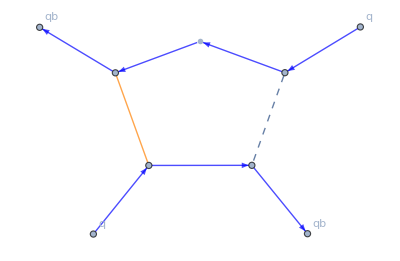
{-1/2,-Graphics-}

```mathematica
PlotDiagram[
Diagramsqbq[[5]],SetupfRG,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
```

```mathematica
symm={
{1,3,Plus}
};
```

```mathematica
symm={
{1,3,Plus}
};
res=ReduceIdenticalFlowDiagrams[Diagramsqbq,DerivativeListqbq,symm];
res//Length
```

100

```mathematica
fullres=SuperindexToFullDiagrams[res,DerivativeListqbq,SetupfRG];
```

```mathematica
Select[res,Not[MemberQ[#,Π,Infinity]]&&Not[MemberQ[#,σ,Infinity]]&]
```

{{Prefactor→{4},<|type→Regulatordot,indices→{{A,{i}},{A,{j}}}|>,<|type→Propagator,indices→{{A,{a83$471978}},{A,{i}}}|>,<|type→nPoint,indices→{{A,{a83$471978}},{qb,{p4,{d4,c4,f4}}},{q,{a83$471979}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{a83$471979}},{qb,{a83$471910}}}|>,<|type→nPoint,indices→{{A,{a83$471911}},{qb,{a83$471910}},{q,{p3,{d3,c3,f3}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471892}},{A,{a83$471911}}}|>,<|type→nPoint,indices→{{A,{a83$471892}},{qb,{p2,{d2,c2,f2}}},{q,{a83$471893}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{a83$471893}},{qb,{a83$471882}}}|>,<|type→nPoint,indices→{{A,{a83$471883}},{qb,{a83$471882}},{q,{p1,{p1,c1,f1}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471883}},{A,{j}}}|>},{Prefactor→{2},<|type→Regulatordot,indices→{{A,{i}},{A,{j}}}|>,<|type→Propagator,indices→{{A,{a83$471910}},{A,{i}}}|>,<|type→nPoint,indices→{{A,{a83$471910}},{qb,{a83$471911}},{q,{p3,{d3,c3,f3}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{a83$471984}},{qb,{a83$471911}}}|>,<|type→nPoint,indices→{{A,{a83$471985}},{qb,{p4,{d4,c4,f4}}},{q,{a83$471984}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471892}},{A,{a83$471985}}}|>,<|type→nPoint,indices→{{A,{a83$471892}},{qb,{p2,{d2,c2,f2}}},{q,{a83$471893}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{a83$471893}},{qb,{a83$471882}}}|>,<|type→nPoint,indices→{{A,{a83$471883}},{qb,{a83$471882}},{q,{p1,{p1,c1,f1}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471883}},{A,{j}}}|>},{Prefactor→{-2},<|type→Regulatordot,indices→{{A,{i}},{A,{j}}}|>,<|type→Propagator,indices→{{A,{a83$471892}},{A,{i}}}|>,<|type→nPoint,indices→{{A,{a83$471892}},{qb,{p2,{d2,c2,f2}}},{q,{a83$471893}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{a83$471893}},{qb,{a83$471916}}}|>,<|type→nPoint,indices→{{A,{a83$471917}},{qb,{a83$471916}},{q,{p3,{d3,c3,f3}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471882}},{A,{a83$471917}}}|>,<|type→nPoint,indices→{{A,{a83$471882}},{qb,{a83$471883}},{q,{p1,{p1,c1,f1}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{a83$472054}},{qb,{a83$471883}}}|>,<|type→nPoint,indices→{{A,{a83$472055}},{qb,{p4,{d4,c4,f4}}},{q,{a83$472054}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$472055}},{A,{j}}}|>},{Prefactor→{-4},<|type→Regulatordot,indices→{{qb,{i}},{q,{j}}}|>,<|type→Propagator,indices→{{q,{a83$471978}},{qb,{i}}}|>,<|type→nPoint,indices→{{A,{a83$471979}},{qb,{p4,{d4,c4,f4}}},{q,{a83$471978}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471910}},{A,{a83$471979}}}|>,<|type→nPoint,indices→{{A,{a83$471910}},{qb,{a83$471911}},{q,{p3,{d3,c3,f3}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{a83$471892}},{qb,{a83$471911}}}|>,<|type→nPoint,indices→{{A,{a83$471893}},{qb,{p2,{d2,c2,f2}}},{q,{a83$471892}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471882}},{A,{a83$471893}}}|>,<|type→nPoint,indices→{{A,{a83$471882}},{qb,{a83$471883}},{q,{p1,{p1,c1,f1}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{j}},{qb,{a83$471883}}}|>},{Prefactor→{-4},<|type→Regulatordot,indices→{{qb,{i}},{q,{j}}}|>,<|type→Propagator,indices→{{q,{a83$472036}},{qb,{i}}}|>,<|type→nPoint,indices→{{A,{a83$472037}},{qb,{p4,{d4,c4,f4}}},{q,{a83$472036}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471892}},{A,{a83$472037}}}|>,<|type→nPoint,indices→{{A,{a83$471892}},{qb,{p2,{d2,c2,f2}}},{q,{a83$471893}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{a83$471893}},{qb,{a83$471916}}}|>,<|type→nPoint,indices→{{A,{a83$471917}},{qb,{a83$471916}},{q,{p3,{d3,c3,f3}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{A,{a83$471882}},{A,{a83$471917}}}|>,<|type→nPoint,indices→{{A,{a83$471882}},{qb,{a83$471883}},{q,{p1,{p1,c1,f1}}}},nPoint→3,spec→none|>,<|type→Propagator,indices→{{q,{j}},{qb,{a83$471883}}}|>}}

```mathematica
ReduceIdenticalFlowDiagrams[Diagramsqbq];
SuperindexToFullDiagrams[%,DerivativeListqbq,SetupfRG]
```

{{-GAA[{-q,v$37958,c$37958,q,v$37938,c$37938}] GAA[{q,v$37942,c$37942,-q,v$37935,c$37935}] Gqqb[{p-q,d$37949,c$37949,f$37949,-p+q,d$37954,c$37954,f$37954}] RdotAA[{-q,v$37935,c$37935,q,v$37938,c$37938}] ΓAqbq[{-q,v$37958,c$37958,-p+q,d$37954,c$37954,f$37954,p,d1,c1,f1}] ΓAqbq[{q,v$37942,c$37942,-p,d2,c2,f2,p-q,d$37949,c$37949,f$37949}]},{-GAA[{-p+q,v$38013,c$38013,p-q,v$38007,c$38007}] Gqqb[{q,d$37998,c$37998,f$37998,-q,d$38019,c$38019,f$38019}] Gqqb[{q,d$38002,c$38002,f$38002,-q,d$37995,c$37995,f$37995}] Rdotqbq[{-q,d$37995,c$37995,f$37995,q,d$37998,c$37998,f$37998}] ΓAqbq[{p-q,v$38007,c$38007,-p,d2,c2,f2,q,d$38002,c$38002,f$38002}] ΓAqbq[{-p+q,v$38013,c$38013,-q,d$38019,c$38019,f$38019,p,d1,c1,f1}]},{-Gqqb[{q,d$38058,c$38058,f$38058,-q,d$38079,c$38079,f$38079}] Gqqb[{q,d$38062,c$38062,f$38062,-q,d$38055,c$38055,f$38055}] GΠΠ[{-p+q,a$38073,p-q,a$38067}] Rdotqbq[{-q,d$38055,c$38055,f$38055,q,d$38058,c$38058,f$38058}] ΓΠqbq[{p-q,a$38067,-p,d2,c2,f2,q,d$38062,c$38062,f$38062}] ΓΠqbq[{-p+q,a$38073,-q,d$38079,c$38079,f$38079,p,d1,c1,f1}]},{-Gqqb[{q,d$38118,c$38118,f$38118,-q,d$38137,c$38137,f$38137}] Gqqb[{q,d$38122,c$38122,f$38122,-q,d$38115,c$38115,f$38115}] Gσσ[{-p+q,p-q}] Rdotqbq[{-q,d$38115,c$38115,f$38115,q,d$38118,c$38118,f$38118}] Γσqbq[{p-q,-p,d2,c2,f2,q,d$38122,c$38122,f$38122}] Γσqbq[{-p+q,-q,d$38137,c$38137,f$38137,p,d1,c1,f1}]},{-Gqqb[{p-q,d$38187,c$38187,f$38187,-p+q,d$38192,c$38192,f$38192}] GΠΠ[{-q,a$38196,q,a$38176}] GΠΠ[{q,a$38180,-q,a$38173}] RdotΠΠ[{-q,a$38173,q,a$38176}] ΓΠqbq[{-q,a$38196,-p+q,d$38192,c$38192,f$38192,p,d1,c1,f1}] ΓΠqbq[{q,a$38180,-p,d2,c2,f2,p-q,d$38187,c$38187,f$38187}]},{-Gqqb[{p-q,d$38244,c$38244,f$38244,-p+q,d$38249,c$38249,f$38249}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσqbq[{-q,-p+q,d$38249,c$38249,f$38249,p,d1,c1,f1}] Γσqbq[{q,-p,d2,c2,f2,p-q,d$38244,c$38244,f$38244}]},{-1/2 GΠΠ[{-q,a$38302,q,a$38292}] GΠΠ[{q,a$38296,-q,a$38289}] RdotΠΠ[{-q,a$38289,q,a$38292}] ΓΠΠqbq[{q,a$38296,-q,a$38302,-p,d2,c2,f2,p,d1,c1,f1}]},{-1/2 Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσσqbq[{q,-q,-p,d2,c2,f2,p,d1,c1,f1}]}}

## End the package

```mathematica
End[]

EndPackage[]
```